{}

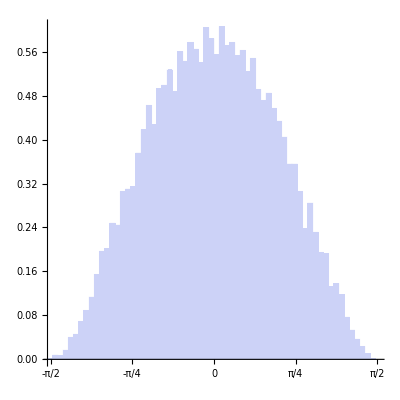
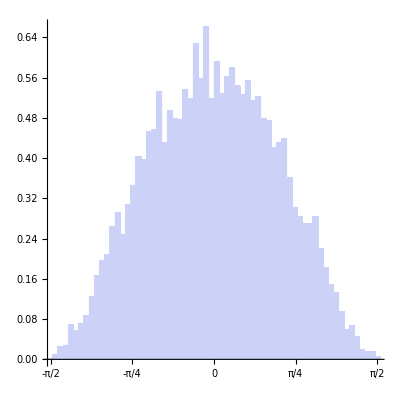
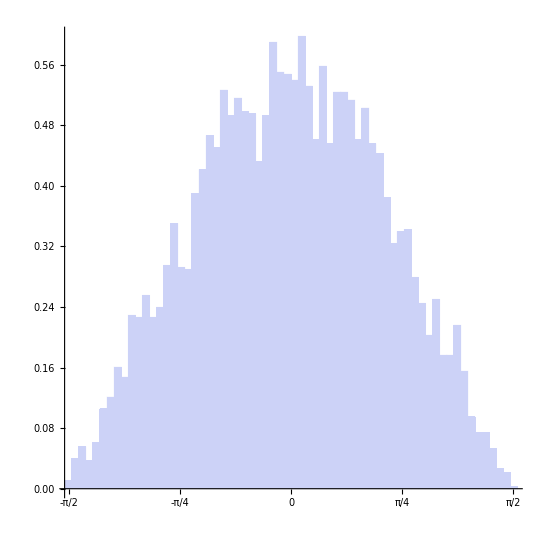
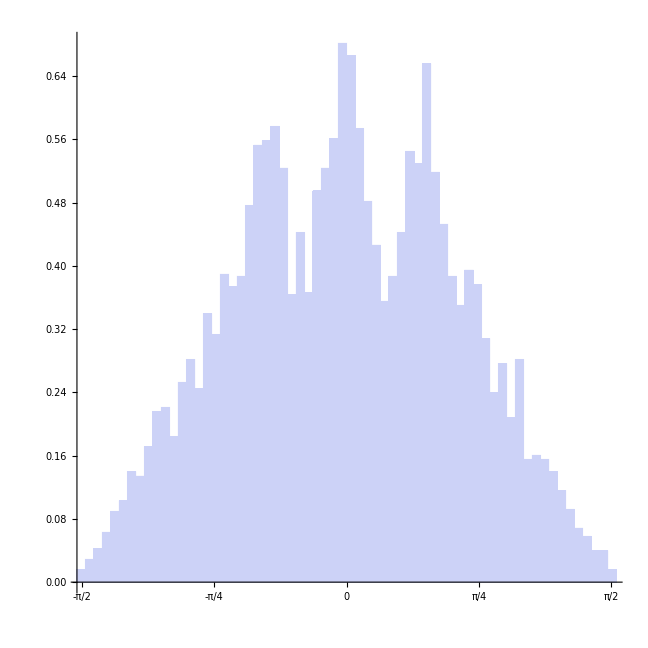
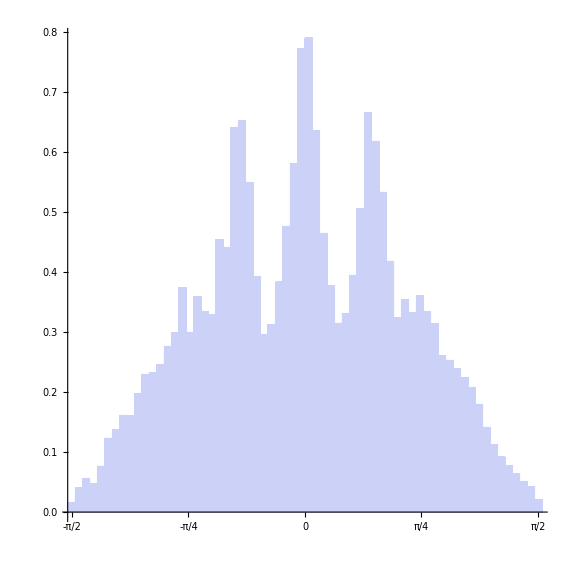
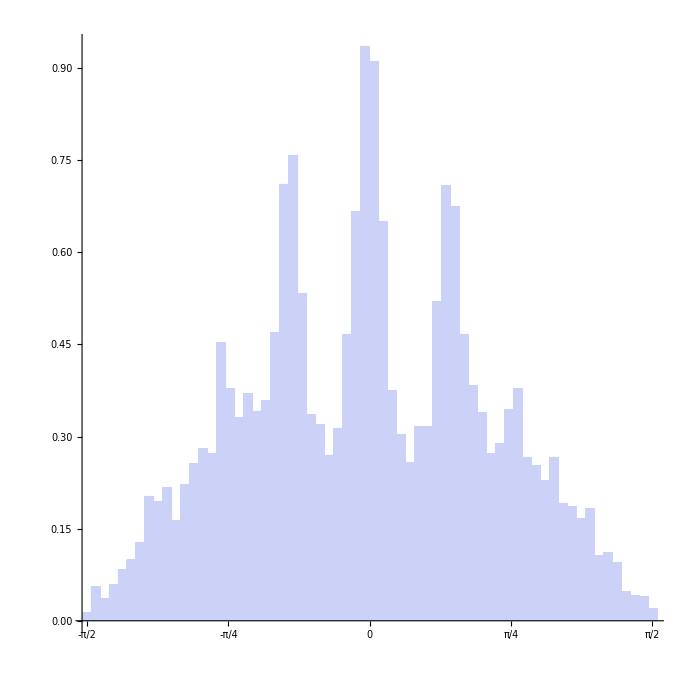
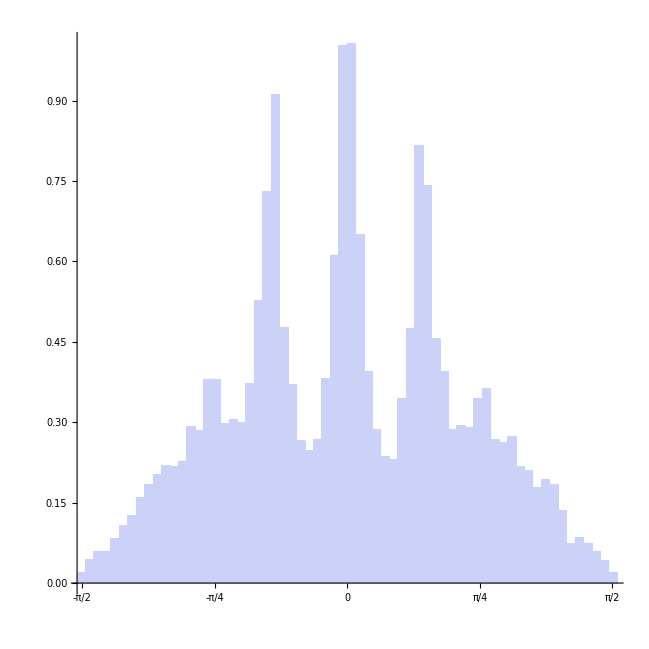
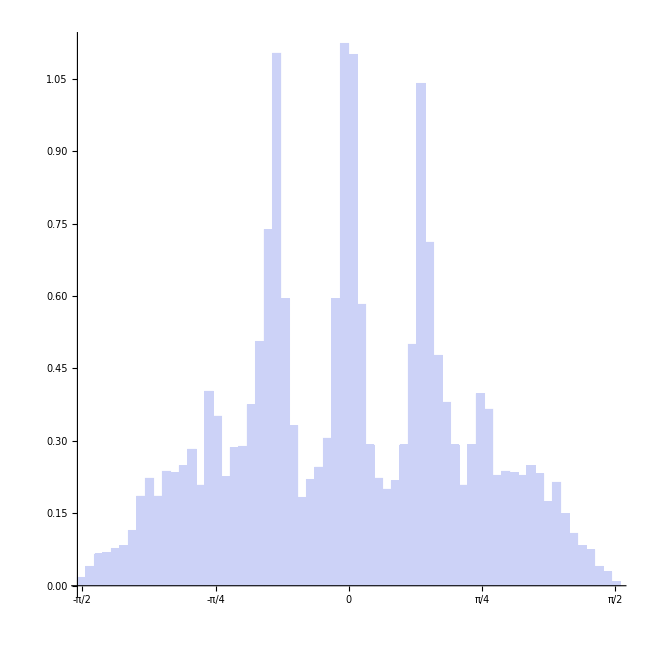
{-Graphics-1,-Graphics-2.5,-Graphics-5,-Graphics-7.5,-Graphics-10,-Graphics-12.5,-Graphics-15,-Graphics-20,-Graphics-30,-Graphics-40,-Graphics-50,-Graphics-60,-Graphics-70,-Graphics-80}

```mathematica
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40,50,60,70,80};
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40,50,60,70,80};
yoyoyo = {}
Do[
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M"<> ToString[MEMVALUE]<>".dat"]];
AppendTo[yoyoyo,Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->30},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}]}],ToString[MEMVALUE],{{Right,Top}}]],
{MEMVALUE,MEMORYLIST}]
yoyoyo
```